```mathematica
mat = {{2^(1/2) u1, 2^(1/2) u2}, {u2, u1 - Pi^2/4}};
mat //MatrixForm
```

(√2 u1 | √2 u2
u2 | -π^2/4+u1)

```mathematica
eigs = Eigenvalues[mat]//Simplify
```

{1/8 (-π^2+4 u1+4 √2 u1-√(π^4+8 (-1+√2) π^2 u1+(48-32 √2) u1^2+64 √2 u2^2)),1/8 (-π^2+4 u1+4 √2 u1+√(π^4+8 (-1+√2) π^2 u1+(48-32 √2) u1^2+64 √2 u2^2))}

```mathematica
(*Solve[eigs[[2]]==0, u1]//Flatten//Simplify*)
foldline = First[Solve[eigs[[2]]==0, u1]]//Flatten//Simplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{u1→1/8 (π^2-√(π^4+64 u2^2))}

```mathematica
ParametricPlot[{u1,u2} /. foldline,{u2, -10, 10}]
```

-Graphics-

```mathematica
critmanif[u1_, u2_] :={{2^(1/2)u1^2+ 2^(1/2)u2^2},{-Pi^2/4 u2+u1 u2}};
{v1line, v2line} =critmanif[u1, u2]/.foldline//Flatten//Simplify
Plot[{v1line, v2line}, {u2, -10, 10}, PlotLabels->Automatic, AxesLabel->Automatic]
```

{(64 u2^2+(π^2-√(π^4+64 u2^2))^2)/(32 √2),-1/8 u2 (π^2+√(π^4+64 u2^2))}

-Graphics-

```mathematica
Solve[v1line ==v1, u2]//Simplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{u2→-(√(-π^4+32 √2 v1-π^2 √(π^4+64 √2 v1)))/(8 √2)},{u2→(√(-π^4+32 √2 v1-π^2 √(π^4+64 √2 v1)))/(8 √2)},{u2→-(√(-π^4+32 √2 v1+π^2 √(π^4+64 √2 v1)))/(8 √2)},{u2→(√(-π^4+32 √2 v1+π^2 √(π^4+64 √2 v1)))/(8 √2)}}

```mathematica
mat3d = {{2^(1/2)u1, 2^(1/2)u2, 2^(1/2)u3}, {2^(1/2)u2, 1/4b2+2^(1/2)u1+u3, u2}, {2^(1/2)u3, u2, 1/4 b3+2^(1/2)u1}}/. {b2->-Pi^2, b3->-4 Pi^2};
mat3d //MatrixForm
```

(√2 u1 | √2 u2 | √2 u3
√2 u2 | -π^2/4+√2 u1+u3 | u2
√2 u3 | u2 | -π^2+√2 u1)

```mathematica
mat3d // Eigenvalues //Simplify
```

{1/4 Root[-16 √2 π^4 u1+160 π^2 u1^2-128 √2 u1^3-128 π^2 u2^2+192 √2 u1 u2^2+64 √2 π^2 u1 u3-128 u1^2 u3-256 u2^2 u3-32 π^2 u3^2+128 √2 u1 u3^2+128 u3^3+(4 π^4-40 √2 π^2 u1+96 u1^2-48 u2^2-16 π^2 u3+32 √2 u1 u3-32 u3^2) #1+(5 π^2-12 √2 u1-4 u3) #1^2+#1^3&,1],1/4 Root[-16 √2 π^4 u1+160 π^2 u1^2-128 √2 u1^3-128 π^2 u2^2+192 √2 u1 u2^2+64 √2 π^2 u1 u3-128 u1^2 u3-256 u2^2 u3-32 π^2 u3^2+128 √2 u1 u3^2+128 u3^3+(4 π^4-40 √2 π^2 u1+96 u1^2-48 u2^2-16 π^2 u3+32 √2 u1 u3-32 u3^2) #1+(5 π^2-12 √2 u1-4 u3) #1^2+#1^3&,2],1/4 Root[-16 √2 π^4 u1+160 π^2 u1^2-128 √2 u1^3-128 π^2 u2^2+192 √2 u1 u2^2+64 √2 π^2 u1 u3-128 u1^2 u3-256 u2^2 u3-32 π^2 u3^2+128 √2 u1 u3^2+128 u3^3+(4 π^4-40 √2 π^2 u1+96 u1^2-48 u2^2-16 π^2 u3+32 √2 u1 u3-32 u3^2) #1+(5 π^2-12 √2 u1-4 u3) #1^2+#1^3&,3]}

```mathematica
- Collect[CharacteristicPolynomial[mat3d,x],x]
```

-(π^4 u1)/(2 √2)+(5 π^2 u1^2)/2-2 √2 u1^3-2 π^2 u2^2+3 √2 u1 u2^2+√2 π^2 u1 u3-2 u1^2 u3-4 u2^2 u3-(π^2 u3^2)/2+2 √2 u1 u3^2+2 u3^3-(-π^4/4+(5 π^2 u1)/(√2)-6 u1^2+3 u2^2+π^2 u3-2 √2 u1 u3+2 u3^2) x-(-(5 π^2)/4+3 √2 u1+u3) x^2+x^3

```mathematica
b=-(-(5 π^2)/4+3 √2 u1+u3);
c=-(-π^4/4+(5 π^2 u1)/(√2)-6 u1^2+3 u2^2+π^2 u3-2 √2 u1 u3+2 u3^2) ;
d=-(π^4 u1)/(2 √2)+(5 π^2 u1^2)/2-2 √2 u1^3-2 π^2 u2^2+3 √2 u1 u2^2+√2 π^2 u1 u3-2 u1^2 u3-4 u2^2 u3-(π^2 u3^2)/2+2 √2 u1 u3^2+2 u3^3;
RegionPlot3D[{d>0 ,b c > d},{u1, -3, 1}, {u2, -5, 5}, {u3, -5, 5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Show[ContourPlot3D[{b==0,d==0 ,b c == d},{u1, -3, 0}, {u2, -5, 5}, {u3, -5, 5},AxesLabel->Automatic, Mesh->None,ContourStyle->Opacity[0.8]],ParametricPlot3D[{u1, 0, 0},{u1, -3, 0},PlotStyle->{Red,Thick} ]]
```

-Graphics3D-

```mathematica
b c - d/.{u2->0, u3->0, u1->-0.01}//Simplify
b/.{u2->0, u3->0, u1->-0.01}//Simplify
d/.{u2->0, u3->0, u1->-0.01}//Simplify
```

305.448

12.3794

0.346863

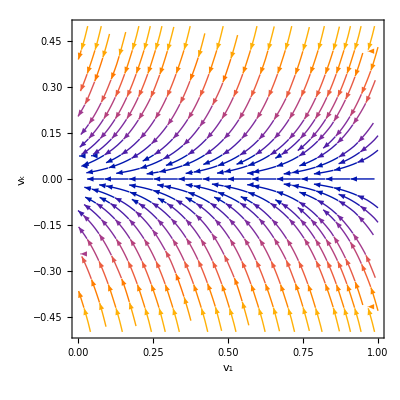

```mathematica
StreamPlot[{-1,-8 v2},{v1, 0, 1}, {v2, -0.5, 0.5},FrameLabel->{Subscript[v, 1],Subscript[v, k]}]
```